```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"]
```

C:\Users\pglpm\repositories\genobayes\scripts2

```mathematica
diffev=-0.0260880661493155;
diffsd=0.0116846434125515;
```

```mathematica
nd[x_,m_,s_]=PDF[NormalDistribution[m,s],x];
```

```mathematica
fnd[x_,m_,s_]=FS[nd[x,m,s]+nd[-x,m,s]];
```

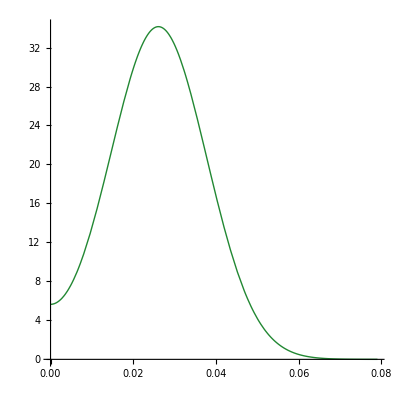

```mathematica
plot=Plot[fnd[x,diffev,diffsd],{x,0,diffev+9*diffsd},PlotStyle->green,PlotRange->{All,{0,All}},Axes->{False,True},Frame->Auto,ImageSize->a4longside,AspectRatio->1,FrameLabel->{Abs[Δ f],"p"[Abs[Δ f]]}]
```

```mathematica
Export["example_absdiff.pdf",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

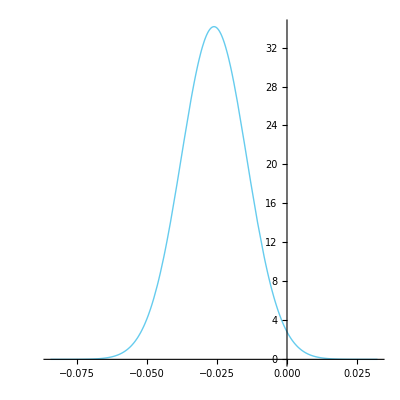

```mathematica
plot=Plot[nd[x,diffev,diffsd],{x,diffev-5*diffsd,diffev+5*diffsd},AspectRatio->1,AxesStyle->{None,{Thick,red,Dashed}},PlotRange->{All,{0,All}},Axes->{False,True},Frame->Auto,ImageSize->a4longside,FrameLabel->{Δ f,"p"[Δ f]}]
```

```mathematica
Export["example_diff.pdf",plot,(*ImageSize->a5rsize,*)ImageResolution->400];
```

```mathematica
Integrate[nd[x,diffev,diffsd],{x,-0.01,0.01}]
```

0.0832726

```mathematica
1-%
```

0.916727

```mathematica
Quantile[NormalDistribution[diffev,diffsd],{0.05,0.95}]
```

{-0.0453076,-0.00686854}

```mathematica
q0[y_]=Assuming[y>0,FS@Re[Integrate[nd[x,diffev,diffsd],{x,-Infinity,-y},Assumptions->y>0]+Integrate[nd[x,diffev,diffsd],{x,y,+Infinity},Assumptions->y>0]]]
```

1.+0.5 Erf[1.57874-60.5159 y]-0.5 Erf[1.57874+60.5159 y]

```mathematica
q1[y_,m_,s_]=Assuming[(y>0&&s>0&&Element[m,Reals]),FS[Integrate[nd[x,m,s],{x,-Infinity,-y},Assumptions->(y>0&&s>0&&Element[m,Reals])]+Integrate[nd[x,m,s],{x,y,+Infinity},Assumptions->(y>0&&s>0&&Element[m,Reals])]]]
```

1/2 (1+Erf[(m-y)/(√2 s)]+Erfc[(m+y)/(√2 s)])

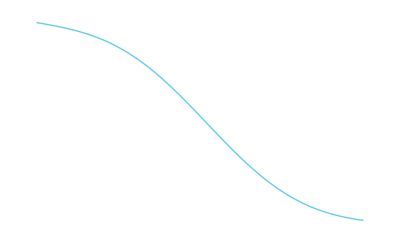

```mathematica
Plot[q1[y,diffev,diffsd],{y,0,0.05}]
```

```mathematica
FindRoot[q1[y,diffev,diffsd]==0.9,{y,0}]
```

{y→0.0111612}

```mathematica
ArgMin[(q1[y,diffev,diffsd]-0.9)^2,{y,0.5}]
```

ArgMin[(-0.9+1/2 (1+Erf[60.5159 (-0.0260881-y)]+Erfc[60.5159 (-0.0260881+y)]))^2,{y,0.5}]

```mathematica
ArgMin[(q1[y,0,0.7]-0.9)^2,y]
```

0.0879629

```mathematica
mean[m_,s_]=Assuming[Element[m,Reals]&&s>0,FS@Expectation[Abs[x],Distributed[x,NormalDistribution[m,s]]]]
```

```mathematica
mean[diffev,diffsd]
```

0.0261921

```mathematica
median[y_,m_,s_]=Assuming[y>0&&Element[m,Reals]&&s>0,FS@Integrate[fnd[x,m,s],{x,0,y},Assumptions->y>0&&Element[m,Reals]&&s>0]]
```

1/2 (-Erf[(m-y)/(√2 s)]+Erf[(m+y)/(√2 s)])

```mathematica
ArgMin[{(median[y,diffev,diffsd]-1/2)^2,y<1},y]
```

0.0260882

```mathematica
Solve[%==1/2,y]
```

Solve[1/2 (-Erf[(m-y)/(√2 s)]+Erf[(m+y)/(√2 s)])==1/2,y]

```mathematica
mmsamples=T@{RandomVariate[UniformDistribution[],1000],RandomVariate[UniformDistribution[{0,1/2}],1000]};
```

```mathematica
toplot={mean[Sequence@@#],ArgMin[{(q1[y,Sequence@@#]-0.9)^2,0<y<1},y]}&/@mmsamples;
```

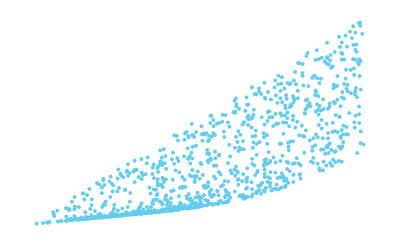

```mathematica
ListPlot[toplot,Joined->False,PlotRange->All]
```

```mathematica
ContourPlot[sig[m,s],{m,0,0.5},{s,0,0.75}]
```

$Aborted

```mathematica
resu={{0.259170041293112,0.2835056871550766},{0.008047270661176678,0.006356164161544898},{0.24602617884103603,0.273099777196446},{0.27249871224939903,0.29400954440503735},{714.7260245717754,714.7260245717754},{266.147127108531,266.147127108531},{2195.7260245717753,3601.7260245717753},{768.147127108531,1425.147127108531}}
```

{{0.25917,0.283506},{0.00804727,0.00635616},{0.246026,0.2731},{0.272499,0.29401},{714.726,714.726},{266.147,266.147},{2195.73,3601.73},{768.147,1425.15}}

```mathematica
%//MF
```

(0.25917 | 0.283506
0.00804727 | 0.00635616
0.246026 | 0.2731
0.272499 | 0.29401
714.726 | 714.726
266.147 | 266.147
2195.73 | 3601.73
768.147 | 1425.15)

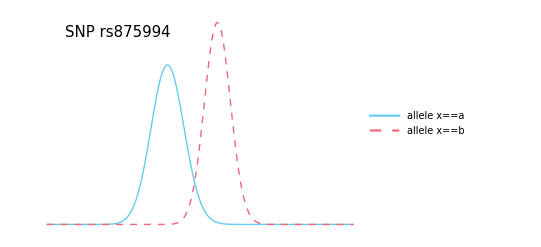

```mathematica
plot=Plot[{bd[x,Sequence@@resu[[7;;8,1]]],bd[x,Sequence@@resu[[7;;8,2]]]},{x,0.2,0.35},PlotRange->All,Axes->None,Frame->Auto,FrameStyle->Directive[Large,Black],ImageSize->a5rsize,FrameLabel->{Subscript[f,HoldForm["O"|x]] ,"p"[HoldForm[Subscript[f,"O" |x]"| data"]]},PlotLegends->Placed[{HoldForm["allele " x==a],HoldForm["allele " x==b]},labelposition[{0.05,0.9}]],Epilog->Text[Style["SNP rs875994",15],Sequence@@textposition[{0.075,0.97}]]]
```

```mathematica
Export["example_distr_condfreqs.pdf",plot,ImageSize->a5rsize]
```

example_distr_condfreqs.pdf